```mathematica
secant[x0_,y0_,x1_,y1_,z_]:=x0-(y0-z)((x1-x0)/(y1-y0));
secantmethod[f_,z_,x1_,x2_,ϵ_,iterations_]:=Block[{k1,k2,k3,y1,y2,count},
k1=x1;
k2=x2;
y1=f[k1];
count=1;
Print[{count,k1,y1}];
y2=f[k2];
count++;
Print[{count,k2,y2}];

While[Abs[k1-k2]>ϵ&&count<iterations,
k3=secant[k1,y1,k2,y2,z];
k1=k2;
y1=y2;

k2=k3;
y2=f[k2];

count++;
Print[{count,k2,y2}];
];
];
halfToUnit[zl_,zr_,z∞_]:=Block[{a,b,c,d,Mlist},
f[z_]:=(a z+b)/(c z+d);
Mlist=Solve[{f[zl]==-1,f[zr]==1,a/c==z∞,a d-b c==1},{a,b,c,d}]⟦1⟧;
({{a, b}, {c, d}})/.Mlist
];
Subscript[f, A_][z_]:=Which[z==∞,If[A⟦2,1⟧==0,∞,A⟦1,1⟧/A⟦2,1⟧],A⟦2,1⟧z+A⟦2,2⟧==0,∞,True,(A⟦1,1⟧z+A⟦1,2⟧)/(A⟦2,1⟧z+A⟦2,2⟧)]
check[A_]:={Subscript[f, A][0],Subscript[f, A][ⅈ],Subscript[f, A][∞]}
```

```mathematica
M0=halfToUnit[(-1+ⅈ)/2,(-9+ⅈ)/2,1/2];
toCirc[A_]:={Subscript[f, A][Subscript[f, M0][0]],Subscript[f, A][Subscript[f, M0][ⅈ]],Subscript[f, A][Subscript[f, M0][∞]]}
```

```mathematica
dist[p_]:=N[Sin[π/p]/Sin[2 π/p]]
R0[p_]:=({{ⅈ-1/dist[p], 1}, {ⅈ/dist[p], -ⅈ}})//FullSimplify
R1[p_]:=({{-1, 2dist[p]+ⅈ}, {0, 1}})//FullSimplify
A1[p_]:=({{1, 0}, {0, 1}})+({{0, 2 dist[p]}, {0, 0}})//FullSimplify
A2[p_]:=({{1, 0}, {0, 1}})+({{ⅈ 1/dist[p], 1/dist[p]}, {1/dist[p], - ⅈ 1/dist[p]}})//FullSimplify
A3[p_]:=({{1, 0}, {0, 1}})+({{0, 0}, {1/dist[p], 0}})//FullSimplify
```

```mathematica
baseSet[p_]:=Join[Table[MatrixPower[R0[p],j].A1[p],{j,1,p-1}],Table[R1[p].MatrixPower[R0[p],j].A1[p],{j,2,p-2}]]//FullSimplify
Subscript[baseSetn, k_][1,p_]:=Map[#+k(A1[p]-({{1, 0}, {0, 1}})).#&,Flatten[{baseSet[p],{A2[p]},{A3[p]}},1]]//FullSimplify
Subscript[baseSetn, k_][2,p_]:=Map[#+k(A2[p]-({{1, 0}, {0, 1}})).#&,Flatten[{baseSet[p],{A1[p]},{A3[p]}},1]]//FullSimplify
Subscript[baseSetn, k_][3,p_]:=Map[#+k(A3[p]-({{1, 0}, {0, 1}})).#&,Flatten[{baseSet[p],{A1[p]},{A2[p]}},1]]//FullSimplify
Subscript[fullSet, k_][p_]:=Join[baseSet[p],Flatten[Table[{Subscript[baseSetn, k1][1,p],Subscript[baseSetn, k1][2,p],Subscript[baseSetn, k1][3,p]},{k1,1,k}],2]]//FullSimplify
Subscript[fullSetRemastered, k_][p_,mat_]:=Map[mat.#.Inverse[mat]&,Subscript[fullSet, k][p]]//FullSimplify
```

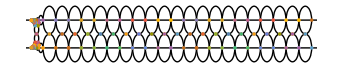

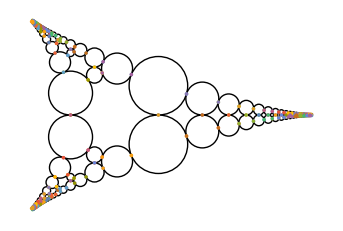

```mathematica
Show[{Graphics[{InfiniteLine[{0,0},{1,0}],InfiniteLine[{0,1},{1,0}],Map[CircleThrough,Map[Transpose,Map[{Re[#],Im[#]}&,Map[check,Subscript[fullSet, 10][3]],1]]]}],ComplexListPlot[Map[check[#]&,Subscript[fullSet, 10][3]],Axes->False]}]
Show[{Graphics[{Map[CircleThrough,Map[Transpose,Map[{Re[#],Im[#]}&,Map[toCirc,Subscript[fullSetRemastered, 10][3,M0]],1]]]}],ComplexListPlot[Map[toCirc[#]&,Subscript[fullSetRemastered, 10][3,M0]],Axes->False]}]
```

```mathematica
λfunc[q_,Nc_,k0_,p0_]:=Block[{generators,M,testM,fancyM,F,fancyF,fancyL,Φ0,Φ1,count},
generators=Subscript[fullSetRemastered, k0][p0,M0];
M=Table[With[{A=N[generators⟦i⟧]},

Table[With[{series =N[Series[(A⟦1,1⟧z+A⟦1,2⟧)^n/(A⟦2,1⟧z+A⟦2,2⟧)^(n+q),{z,0,Nc}]]},Table[SeriesCoefficient[series,s],{s,0,Nc}]],{n,0,Nc}]

],{i,1,Length[generators]}];

fancyM=Table[0,{i,0,(Nc+1)^2-1},{j,0,(Nc+1)^2-1}];
For[m=0,m≤Nc,m++,
Print[m];
For[n=0,n≤Nc,n++,
For[r=0,r≤Nc,r++,
For[s=0,s≤Nc,s++,
If[m≤n,
fancyM⟦(m*(Nc+1))+n+1,(r*(Nc+1))+s+1⟧=∑_(i=1)^Length[generators] M⟦i,m+1,r+1⟧*M⟦i,n+1,s+1⟧;,
fancyM⟦(m*(Nc+1))+n+1,(r*(Nc+1))+s+1⟧=fancyM⟦(n*(Nc+1))+m+1,(s*(Nc+1))+r+1⟧*;
]]]]];

fancyL=Re[fancyM];

Φ0=Table[0,{i,0,(Nc+1)^2-1}];
Φ0⟦1⟧=1;

For[count=1,count≤52,count++,
Φ0=Φ0.fancyL
];
Φ1=Φ0.fancyL;
Φ1⟦1⟧/Φ0⟦1⟧]
```

```mathematica
Timing[secantmethod[λfunc[#,20,100,3]&,1,1.3,1.31,10^-13,12]]
```

0

$Aborted